# Pyr conv rates

```mathematica
myAxesSize=15;
myLabelSize=12;
myImageSize=500;
```

Case 1 - u(x,y,z) = x^2

### Pts extracted from pz

```mathematica
neq={96,704,2304,5376,10400,17856};
h={1,0.5,0.25,0.125,0.125/2,0.125/4};
h1={0.0549425,0.015023,0.00716338,0.00428266,0.00289409,0.00211095};
l2={0.0501596,0.0124746,0.00553585,0.00311179,0.00199075,0.0013821};
semih1={0.0224207,0.00837112,0.00454626,0.00294244,0.00210064,0.00159559};
ptsh1=Table[{h[[i]],h1[[i]]},{i,Length[neq]}];
ptsl2=Table[{h[[i]],l2[[i]]},{i,Length[neq]}];
ptssemih1=Table[{h[[i]],semih1[[i]]},{i,Length[neq]}];
```

### Plots

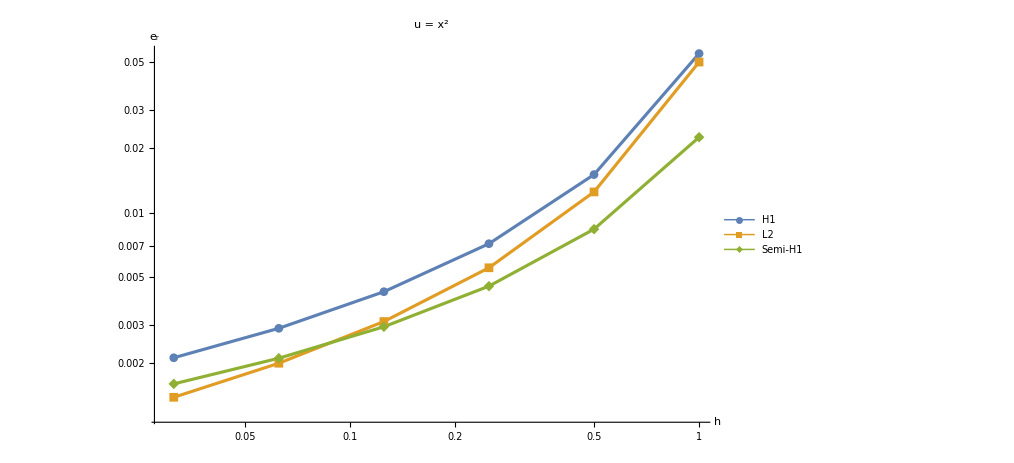

```mathematica
ListLogLogPlot[{ptsh1,ptsl2,ptssemih1},PlotRange->All,PlotStyle->Thickness[0.003],ImageSize->myImageSize 1.5,PlotLabel->Style["u = x^2",14,Black],AxesLabel->{Style["h",myAxesSize,Black],Style["e_r",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"H1","L2","Semi-H1"},{0.75,0.85}]]
```

### Conv rates

```mathematica
convratesh1=Range[Length[neq]-1];
convratesl2=Range[Length[neq]-1];
convratesh1semi=Range[Length[neq]-1];
For[i=1,i≤Length[neq]-1,i++,
convratesh1[[i]]=Log[h1[[i]]/h1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesl2[[i]]=Log[l2[[i]]/l2[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesh1semi[[i]]=Log[semih1[[i]]/semih1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
]
convratesh1
convratesl2
convratesh1semi
```

{1.87075,1.06846,0.742133,0.565397,0.455217}

{2.00753,1.17212,0.83106,0.644433,0.52645}

{1.42134,0.88074,0.627667,0.486184,0.396739}

Case 2 - u(x,y,z) = x^2+y^2+z^2

### Pts extracted from pz

```mathematica
neq={96,704,2304,5376,10400,17856};
h={1,0.5,0.25,0.125,0.125/2,0.125/4};
h1={0.108402,0.028558,0.0132754,0.00777944,0.00517111,0.00371993};
l2={0.103528,0.0258139,0.0114641,0.00644631,0.0041248,0.00286407};
semih1={0.0321418,0.0122149,0.006694,0.00435486,0.00311872,0.00237382};
ptsh1=Table[{h[[i]],h1[[i]]},{i,Length[neq]}];
ptsl2=Table[{h[[i]],l2[[i]]},{i,Length[neq]}];
ptssemih1=Table[{h[[i]],semih1[[i]]},{i,Length[neq]}];
```

### Plots

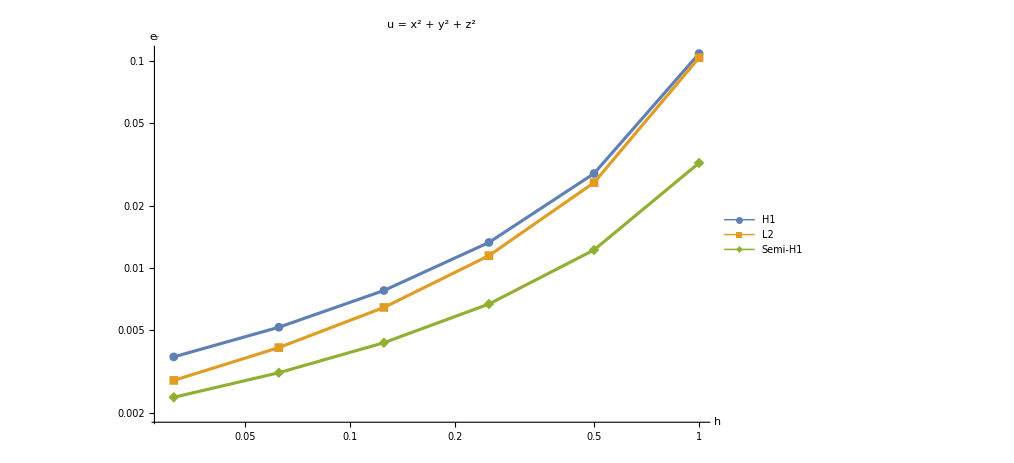

```mathematica
ListLogLogPlot[{ptsh1,ptsl2,ptssemih1},PlotRange->All,PlotStyle->Thickness[0.003],ImageSize->myImageSize 1.5,PlotLabel->Style["u = x^2 + y^2 + z^2",14,Black],AxesLabel->{Style["h",myAxesSize,Black],Style["e_r",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"H1","L2","Semi-H1"},{0.75,0.85}]]
```

### Conv rates

```mathematica
convratesh1=Range[Length[neq]-1];
convratesl2=Range[Length[neq]-1];
convratesh1semi=Range[Length[neq]-1];
For[i=1,i≤Length[neq]-1,i++,
convratesh1[[i]]=Log[h1[[i]]/h1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesl2[[i]]=Log[l2[[i]]/l2[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesh1semi[[i]]=Log[semih1[[i]]/semih1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
]
convratesh1
convratesl2
convratesh1semi
```

{1.92442,1.10514,0.771017,0.589192,0.475199}

{2.0038,1.17103,0.830578,0.644149,0.526257}

{1.39581,0.867702,0.620242,0.481672,0.393743}